# Project 4

### Parameters :

```mathematica
Subscript[ω, 1]=Sqrt[0.29575];
Subscript[ω, 2]=Sqrt[2.12581];
λ=-0.1116;
η=0.08414;
V12[q1_,q2_]:=λ*(q2^2*q1+η*q1^3);
nn = 20; (* Basis set number *)
```

### Matrices parameters

```mathematica
vecs1=ConstantArray[1, {20, 20}];
vecs2 =ConstantArray[1, {20, 20}];
vals1=ConstantArray[1, {5,20}];
vals2 =ConstantArray[1, {5,20}];
(* cc=ConstantArray[0, {20, 20}]; *)
cc1=ConstantArray[1, {20, 20}];
cc2=ConstantArray[1, {20, 20}];
H1v=ConstantArray[1, {20, 20}];
H2v=ConstantArray[1, {20, 20}];
H1k=ConstantArray[1, {20, 20}];
H2k=ConstantArray[1, {20, 20}];
Ek=ConstantArray[1,5];
cpp=ConstantArray[1,5];
c1=ConstantArray[1, 20];
c2=ConstantArray[1, 20];
```

### Loop - HO Basis Set

```mathematica
Subscript[ϕ, 1]=Table[(1/Sqrt[2^i*i!])*(Subscript[ω, 1]/Pi)^(1/4)*Exp[-Subscript[ω, 1]*q1^2/2]*HermiteH[i,Sqrt[Subscript[ω, 1]]*q1],{i,0,nn-1}];
Subscript[ϕ, 2]=Table[(1/Sqrt[2^i*i!])*(Subscript[ω, 2]/Pi)^(1/4)*Exp[-Subscript[ω, 2]*q2^2/2]*HermiteH[i,Sqrt[Subscript[ω, 2]]*q2],{i,0,nn-1}];
vecs1=ConstantArray[1, {20, 20}];
vecs2 =ConstantArray[1, {20, 20}];
(* cc=ConstantArray[0, {20, 20}]; *)
cc1=ConstantArray[1, {20, 20}];
cc2=ConstantArray[1, {20, 20}];
H1v=ConstantArray[1, {20, 20}];
H2v=ConstantArray[1, {20, 20}];
H1k=ConstantArray[1, {20, 20}];
H2k=ConstantArray[1, {20, 20}];
Ek=ConstantArray[1,5];
c1=ConstantArray[1, 20];
c2=ConstantArray[1, 20];
cpp=ConstantArray[0,{5,nn}];
For[kloop=1,kloop<=5,kloop++,
For[ii=1,ii<=Length[Subscript[ϕ, 1][q1]],ii++,
c1[[ii]]=Integrate[Subscript[ϕ, 2][[ii]]^2*V12[q1,q2],{q2,-∞,∞}];
c2[[ii]]=Integrate[Subscript[ϕ, 1][[ii]]^2*V12[q1,q2],{q1,-∞,∞}];
];
For[ii=1,ii<=Length[Subscript[ϕ, 1]],ii++,
For[jj=ii,jj<=Length[Subscript[ϕ, 2]],jj++,
cc1[[ii,jj]]=Integrate[Subscript[ϕ, 1][[ii]]*Total[c1]*Subscript[ϕ, 1][[jj]],{q1,-∞,∞}];
cc2[[ii,jj]]=Integrate[Subscript[ϕ, 2][[ii]]*Total[c2]*Subscript[ϕ, 2][[jj]],{q2,-∞,∞}];
cc1[[jj,ii]]=cc1[[ii,jj]];
cc2[[jj,ii]]=cc2[[ii,jj]];
H1v[[ii,jj]]=Integrate[Subscript[ϕ, 1][[ii]]*0.5*Subscript[ω, 1]^2*q1^2*Subscript[ϕ, 1][[jj]],{q1,-∞,∞}];
H2v[[ii,jj]]=Integrate[Subscript[ϕ, 2][[ii]]*0.5*Subscript[ω, 2]^2*q2^2*Subscript[ϕ, 2][[jj]],{q2,-∞,∞}];
H1v[[jj,ii]]=H1v[[ii,jj]];
H2v[[jj,ii]]=H2v[[ii,jj]];
H1k[[ii,jj]]=-0.5*Integrate[Subscript[ϕ, 1][[ii]]*D[D[Subscript[ϕ, 1][[jj]],q1],q1],{q1,-∞,∞}];
H2k[[ii,jj]]=-0.5*Integrate[Subscript[ϕ, 2][[ii]]*D[D[Subscript[ϕ, 2][[jj]],q2],q2],{q2,-∞,∞}];
H1k[[jj,ii]]=H1k[[ii,jj]];
H2k[[jj,ii]]=H2k[[ii,jj]];
]
];
{vals1[[kloop]],vecs1}=Eigensystem[cc1+H1k+H1v];
{vals2[[kloop]],vecs2}=Eigensystem[cc2+H2k+H2v];
Subscript[ϕ, 1]=Table[vecs1[[Position[vals1[[kloop]],_?Positive][[Length[Position[vals1[[kloop]],_?Positive]]]][[1]],i]]*Subscript[ϕ, 1][[i]],{i,1,nn}];
Subscript[ϕ, 2]=Table[vecs2[[Position[vals2[[kloop]],_?Positive][[Length[Position[vals2[[kloop]],_?Positive]]]][[1]],i]]*Subscript[ϕ, 2][[i]],{i,1,nn}];
For[ii=1,ii<=Length[ϕ1],ii++, cpp[[kloop,ii]]=Integrate[Subscript[ϕ, 1][[ii]]^2*Integrate[Subscript[ϕ, 2][[ii]]^2*V12[q1,q2],{q2,-∞,∞}],{q1,-∞,∞}]];
Ek[[kloop]]=Extract[vals1[[kloop]],Position[vals1[[kloop]],_?Positive]][[Length[Extract[vals1[[kloop]],Position[vals1[[kloop]],_?Positive]]]]]+Extract[vals2[[kloop]],Position[vals2[[kloop]],_?Positive]][[Length[Extract[vals2[[kloop]],Position[vals2[[kloop]],_?Positive]]]]]-Total[cpp[[kloop]]]; 
]//Timing
```

{754.047,Null}

```mathematica
Ek
```

{9.54602,0.0036251,1.24586×10^-14,28.4313,26.9733,28.4313,26.9733,28.4313}

```mathematica
Ek
```

{38.9935,1.28444×10^-14,1.28444×10^-14,1.28444×10^-14,1.28444×10^-14}

```mathematica
Ek
```

{38.9935,1.28444×10^-14,1.28444×10^-14,1.28444×10^-14,1.28444×10^-14}

```mathematica
Subscript[ω, 1]/2+Subscript[ω, 2]/2
```

1.00092

```mathematica
Plot3D[0.2719145086235746 q1^2+0.7290078874744772 q2^2-0.1116 (0.08414 q1^3+q1 q2^2),{q1,-20,20},{q2,-20,20}]
```

-Graphics3D-

```mathematica
Subscript[ω, 1]*(20+1/2)
```

11.1485

```mathematica
kmx=3;
Subscript[ω, 1]=Sqrt[0.29575];
Subscript[ω, 2]=Sqrt[2.12581];
λ=-0.1116;
η=0.08414;
V12[q1_,q2_]:=λ*(q2^2*q1+η*q1^3);
nn = 20; (* Basis set number *)
L1=Sqrt[2*(30+1/2)/Subscript[ω, 1]]; (*Turning Points*)
L2=Sqrt[2*(30+1/2)/Subscript[ω, 2]];(*Turning Points*)
ϕ1=ConstantArray[1, {kmx+2, nn}];
ϕ2=ConstantArray[1, {kmx+2, nn}];
vecs2 =ConstantArray[1, {nn, nn}];
ϕ1[[1]]=Table[(Sqrt[2/L1])*Sin[i*Pi*(q1+L1/2)/L1],{i,1,nn}];
ϕ2[[1]]=Table[(Sqrt[2/L2])*Sin[i*Pi*(q2+L2/2)/L2],{i,1,nn}];
vecs1=ConstantArray[1, {nn, nn}];
vecs2 =ConstantArray[1, {nn, nn}];
vals1=ConstantArray[1, {kmx,nn}];
vals2 =ConstantArray[1, {kmx,nn}];
(* cc=ConstantArray[0, {20, 20}]; *)
cc1=ConstantArray[1, {nn, nn}];
cc2=ConstantArray[1, {nn, nn}];
H1v=ConstantArray[1, {nn, nn}];
H2v=ConstantArray[1, {nn, nn}];
H1k=ConstantArray[1, {nn, nn}];
H2k=ConstantArray[1, {nn, nn}];
Ek=ConstantArray[1,kmx];
cpp=ConstantArray[1,{kmx,nn}];
c1=ConstantArray[1, nn];
c2=ConstantArray[1,nn];
c22=ConstantArray[1,nn];
For[ii=1,ii<=nn,ii++,
For[jj=ii,jj<=nn,jj++,
H1v[[ii,jj]]=Integrate[ϕ1[[1,ii]]*0.5*Subscript[ω, 1]^2*q1^2*ϕ1[[1,jj]],{q1,-L1/2,L1/2}];
H2v[[ii,jj]]=Integrate[ϕ2[[1,ii]]*0.5*Subscript[ω, 2]^2*q2^2*ϕ2[[1,jj]],{q2,-L2/2,L2/2}];
H1v[[jj,ii]]=H1v[[ii,jj]];
H2v[[jj,ii]]=H2v[[ii,jj]];
H1k[[ii,jj]]=-0.5*Integrate[ϕ1[[1,ii]]*D[D[ϕ1[[1,jj]],q1],q1],{q1,-L1/2,L1/2}];
H2k[[ii,jj]]=-0.5*Integrate[ϕ2[[1,ii]]*D[D[ϕ2[[1,jj]],q2],q2],{q2,-L2/2,L2/2}];
H1k[[jj,ii]]=H1k[[ii,jj]];
H2k[[jj,ii]]=H2k[[ii,jj]];
];
];
{vals1[[1]],vecs1}=Eigensystem[H1k+H1v];
{vals2[[1]],vecs2}=Eigensystem[H2k+H2v];
For[i=1,i<=nn,i++,
ϕ1[[2,i]]=Dot[vecs1[[nn+1-i]],ϕ1[[1]]];
ϕ2[[2,i]]=Dot[vecs2[[nn+1-i]],ϕ2[[1]]];
];
(*ϕ1=Table[vecs1[[Position[vals1[[1]],_?Positive][[Length[Position[vals1[[1]],_?Positive]]]][[1]]]]*ϕ1[[i]],{i,1,nn}];*)
For[kloop=1,kloop<=kmx,kloop++,
For[ii=1,ii<=nn,ii++,
c1[[ii]]=Integrate[ϕ2[[kloop+1,ii]]^2*λ*q2^2,{q2,-L2/2,L2/2}];
c2[[ii]]=Integrate[ϕ1[[kloop+1,ii]]^2*λ*q1,{q1,-L1/2,L1/2}]; 
c22[[ii]]=Integrate[ϕ1[[kloop+1,ii]]^2*λ*η*q1^3,{q1,-L1/2,L1/2}];
]; 
For[ii=1,ii<=nn,ii++,
For[jj=ii,jj<=nn,jj++,
cc1[[ii,jj]]=Integrate[ϕ1[[kloop+1,ii]]*(Total[c1]*q1+λ*η*q1^3)*ϕ1[[kloop+1,jj]],{q1,-L1/2,L1/2}];
cc2[[ii,jj]]=Integrate[ϕ2[[kloop+1,ii]]*(Total[c2]*q2^2+Total[c22])*ϕ2[[kloop+1,jj]],{q2,-L2/2,L2/2}];
cc1[[jj,ii]]=cc1[[ii,jj]];
cc2[[jj,ii]]=cc2[[ii,jj]];
H1v[[ii,jj]]=Integrate[ϕ1[[kloop+1,ii]]*0.5*Subscript[ω, 1]^2*q1^2*ϕ1[[kloop+1,jj]],{q1,-L1/2,L1/2}];
H2v[[ii,jj]]=Integrate[ϕ2[[kloop+1,ii]]*0.5*Subscript[ω, 2]^2*q2^2*ϕ2[[kloop+1,jj]],{q2,-L2/2,L2/2}];
H1v[[jj,ii]]=H1v[[ii,jj]];
H2v[[jj,ii]]=H2v[[ii,jj]];
H1k[[ii,jj]]=-0.5*Integrate[ϕ1[[kloop+1,ii]]*D[D[ϕ1[[kloop+1,jj]],q1],q1],{q1,-L1/2,L1/2}];
H2k[[ii,jj]]=-0.5*Integrate[ϕ2[[kloop,+1ii]]*D[D[ϕ2[[kloop+1,jj]],q2],q2],{q2,-L2/2,L2/2}];
H1k[[jj,ii]]=H1k[[ii,jj]];
H2k[[jj,ii]]=H2k[[ii,jj]];
];
];
{vals1[[kloop]],vecs1}=Eigensystem[cc1+H1k+H1v];
{vals2[[kloop]],vecs2}=Eigensystem[cc2+H2k+H2v];
For[i=1,i<=nn,i++,
ϕ1[[kloop+2,i]]=Dot[vecs1[[nn+1-i]],ϕ1[[kloop+1]]];
ϕ2[[kloop+2,i]]=Dot[vecs2[[nn+1-i]],ϕ2[[kloop+1]]];
];
For[ii=1,ii<=nn,ii++, cpp[[kloop,ii]]=Integrate[ϕ1[[kloop+2,ii]]^2*Integrate[ϕ2[[kloop+2,ii]]^2*V12[q1,q2],{q2,-L2/2,L2/2}],{q1,-L1/2,L1/2}]];
Ek[[kloop]]=Extract[vals1[[kloop]],Position[vals1[[kloop]],_?Positive]][[Length[Extract[vals1[[kloop]],Position[vals1[[kloop]],_?Positive]]]]]+Extract[vals2[[kloop]],Position[vals2[[kloop]],_?Positive]][[Length[Extract[vals2[[kloop]],Position[vals2[[kloop]],_?Positive]]]]]-Total[cpp[[kloop]]]; 
]//Timing
```

$Aborted

```mathematica
Ek
```

{2.48274,0.000251304,40.4443,36.9792,40.4443}

```mathematica
Ek
```

{11.4261,0.00695701,27.6418,25.8973,27.6418,25.8973}

```mathematica
Ek
```

{1.00092,-1.84752×10^-15,36.4675,34.8656,36.4675}

```mathematica
Ek
```

{2.10114,0.0000983242,3.1442×10^-15,4.38743×10^-25,2.06352×10^-30}

```mathematica
kmx=1;
Subscript[ω, 1]=Sqrt[0.29575];
Subscript[ω, 2]=Sqrt[2.12581];
λ=-0.1116;
η=0.08414;
V12[q1_,q2_]:=λ*(q2^2*q1+η*q1^3);
nn = 10; (* Basis set number *)
L1=Sqrt[2*(15+1/2)/Subscript[ω, 1]]; (*Turning Points*)
L2=Sqrt[2*(15+1/2)/Subscript[ω, 2]];(*Turning Points*)
vecs2 =ConstantArray[1, {nn, nn}];
ϕ1=Table[(Sqrt[2/L1])*Sin[i*Pi*(q1+L1/2)/L1],{i,1,nn}];
ϕ2=Table[(Sqrt[2/L2])*Sin[i*Pi*(q2+L2/2)/L2],{i,1,nn}];
vecs1=ConstantArray[1, {nn, nn}];
vecs2 =ConstantArray[1, {nn, nn}];
vals1=ConstantArray[1, {kmx,nn}];
vals2 =ConstantArray[1, {kmx,nn}];
(* cc=ConstantArray[0, {20, 20}]; *)
cc1=ConstantArray[1, {nn, nn}];
cc2=ConstantArray[1, {nn, nn}];
H1v=ConstantArray[1, {nn, nn}];
H2v=ConstantArray[1, {nn, nn}];
H1k=ConstantArray[1, {nn, nn}];
H2k=ConstantArray[1, {nn, nn}];
Ek=ConstantArray[1,kmx];
cpp=ConstantArray[1,{kmx,nn}];
c1=ConstantArray[1, nn];
c2=ConstantArray[1,nn];
c22=ConstantArray[1,nn];
For[ii=1,ii<=nn,ii++,
For[jj=ii,jj<=nn,jj++,
H1v[[ii,jj]]=Integrate[ϕ1[[ii]]*0.5*Subscript[ω, 1]^2*q1^2*ϕ1[[jj]],{q1,-L1/2,L1/2}];
H2v[[ii,jj]]=Integrate[ϕ2[[ii]]*0.5*Subscript[ω, 2]^2*q2^2*ϕ2[[jj]],{q2,-L2/2,L2/2}];
H1v[[jj,ii]]=H1v[[ii,jj]];
H2v[[jj,ii]]=H2v[[ii,jj]];
H1k[[ii,jj]]=-0.5*Integrate[ϕ1[[ii]]*D[D[ϕ1[[jj]],q1],q1],{q1,-L1/2,L1/2}];
H2k[[ii,jj]]=-0.5*Integrate[ϕ2[[ii]]*D[D[ϕ2[[jj]],q2],q2],{q2,-L2/2,L2/2}];
H1k[[jj,ii]]=H1k[[ii,jj]];
H2k[[jj,ii]]=H2k[[ii,jj]];
];
];
{vals1[[1]],vecs1}=Eigensystem[H1k+H1v];
{vals2[[1]],vecs2}=Eigensystem[H2k+H2v];
```

```mathematica
ϕ11=Dot[vecs1[[nn]],ϕ1];
ϕ22=Dot[vecs2[[nn]],ϕ2];
```

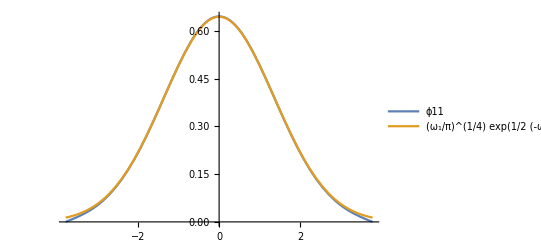

```mathematica
Plot[{ϕ11,(Subscript[ω, 1]/Pi)^(1/4)*Exp[-Subscript[ω, 1]*q1^2/2]*HermiteH[0,Sqrt[Subscript[ω, 1]]*q1]},{q1,-L1/2,L1/2},PlotLegends->"Expressions"]
```

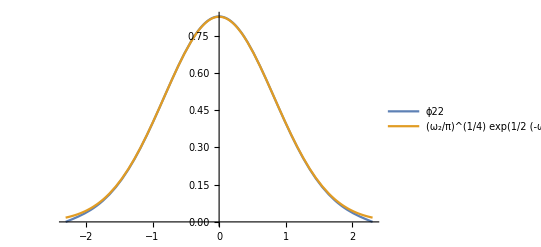

```mathematica
Plot[{ϕ22,(Subscript[ω, 2]/Pi)^(1/4)*Exp[-Subscript[ω, 2]*q2^2/2]*HermiteH[0,Sqrt[Subscript[ω, 2]]*q2]},{q2,-L2/2,L2/2},PlotLegends->"Expressions"]
```